```mathematica
test=stubbornForm
```

<|0→<|signature→0,matrix→{{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{},5,colofour2→z,colortable3→{{-b09+z,b09},{-b01+z,b01},{-b03+z,b03},{-b10+z,b10},{-b08+z,b08},{-b05+z,b05},{-b02+z,b02},{-b07+z,b07},{-b04+z,b04},{-b06+z,b06}},compwhy→Embedding is planar and follows IH,comp→Greater,colofour3→z,colortable4→{{-b09+z,b09},{-b01+z,b01},{-b03+z,b03},{-b10+z,b10},{-b08+z,b08},{-b05+z,b05},{-b02+z,b02},{-b07+z,b07},{-b04+z,b04},{-b06+z,b06}}|>,1893,59048→<|signature→59048,15,colortable4→{1}|>|>
 |  |  |  |

```mathematica
Select[stubbornKeys,#≠K5Key&]//Length
```

50

```mathematica
ListofVars[12]
```

{b01,b02,b16,b17,b18,b19,b20,b03,b04,b05,b07,b14,s01,s03,s05,s06,s07,s08,s09,s10,s11,s12,s13,s14,s15,s16,s17,s18,s19,s20,α,α1,β,β1,γ,γ1,δ,δ1,ϵ,ϵ1,ζ}

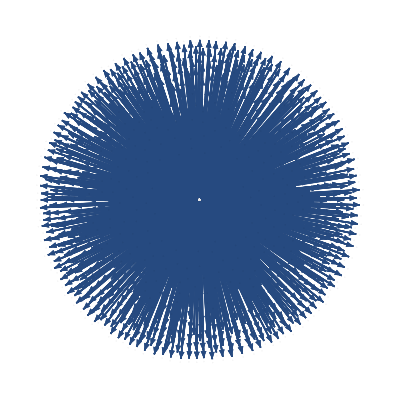

```mathematica
With[
{vars={α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}},Graph[Table [Map[#->jj&,Intersection[ListofVars[jj],vars]],{jj,Select[Keys[test],ContainsAll[ListofVars[#],vars]&]}]//Flatten,VertexSize->Tiny]
]
```

```mathematica
edges1=Table [Map[#->jj&,With[{kk=getAllVariables[test[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]]],{jj,Select[stubbornKeys,#≠K5Key&]}]//Flatten
```

```mathematica
edges1={s01->448,s03->448,γ1->448,s01->7738,γ1->7738,s14->9112,s15->9112,ζ->9112,s13->9598,s15->9598,ζ->9598,s15->9841,s01->11680,s05->11680,ϵ1->11680,s01->11950,ϵ1->11950,s03->22318,γ1->22318,s02->24922,s05->24922,β1->24922,s02->25168,β1->25168,s11->28794,s14->28794,ζ->28794,s14->28795,s12->29272,s13->29272,ζ->29272,s13->29281,s11->29514,s12->29514,ζ->29514,s12->29515,s11->29523,s11->29525,ζ->29525,s12->29533,ζ->29533,s17->29560,γ1->29608,s10->29633,s13->29767,ζ->29767,s09->29797,s14->30253,ζ->30253,s16->30334,s05->31444,ϵ1->31444,s05->31492,β1->31492,ϵ1->31714,β1->31738,s19->31954,s05->31984,s02->33834,s04->33834,δ1->33834,s02->33916,δ1->33916,s03->35406,s04->35406,α1->35406,s03->35434,α1->35434,s04->36030,δ1->36030,s20->36086,δ1->36112,s04->36138,α1->36138,α1->36166,s04->36194,s08->36817,s03->36898,s07->38281,s02->38308,s15->49207,ζ->49207,s18->49210,s06->51475,s01->51478}
```

{s01→448,s03→448,γ1→448,s01→7738,γ1→7738,s14→9112,s15→9112,ζ→9112,s13→9598,s15→9598,ζ→9598,s15→9841,s01→11680,s05→11680,ϵ1→11680,s01→11950,ϵ1→11950,s03→22318,γ1→22318,s02→24922,s05→24922,β1→24922,s02→25168,β1→25168,s11→28794,s14→28794,ζ→28794,s14→28795,s12→29272,s13→29272,ζ→29272,s13→29281,s11→29514,s12→29514,ζ→29514,s12→29515,s11→29523,s11→29525,ζ→29525,s12→29533,ζ→29533,s17→29560,γ1→29608,s10→29633,s13→29767,ζ→29767,s09→29797,s14→30253,ζ→30253,s16→30334,s05→31444,ϵ1→31444,s05→31492,β1→31492,ϵ1→31714,β1→31738,s19→31954,s05→31984,s02→33834,s04→33834,δ1→33834,s02→33916,δ1→33916,s03→35406,s04→35406,α1→35406,s03→35434,α1→35434,s04→36030,δ1→36030,s20→36086,δ1→36112,s04→36138,α1→36138,α1→36166,s04→36194,s08→36817,s03→36898,s07→38281,s02→38308,s15→49207,ζ→49207,s18→49210,s06→51475,s01→51478}

```mathematica
edges2={s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19}
```

{s06<->s15,s07<->s12,s08<->s14,s09<->s13,s10<->s11,s11<->s20,s12<->s17,s13<->s19,s14<->s16,s15<->s18,s01<->s06,s01<->s18,s02<->s07,s02<->s17,s03<->s08,s03<->s16,s04<->s10,s04<->s20,s05<->s09,s05<->s19}

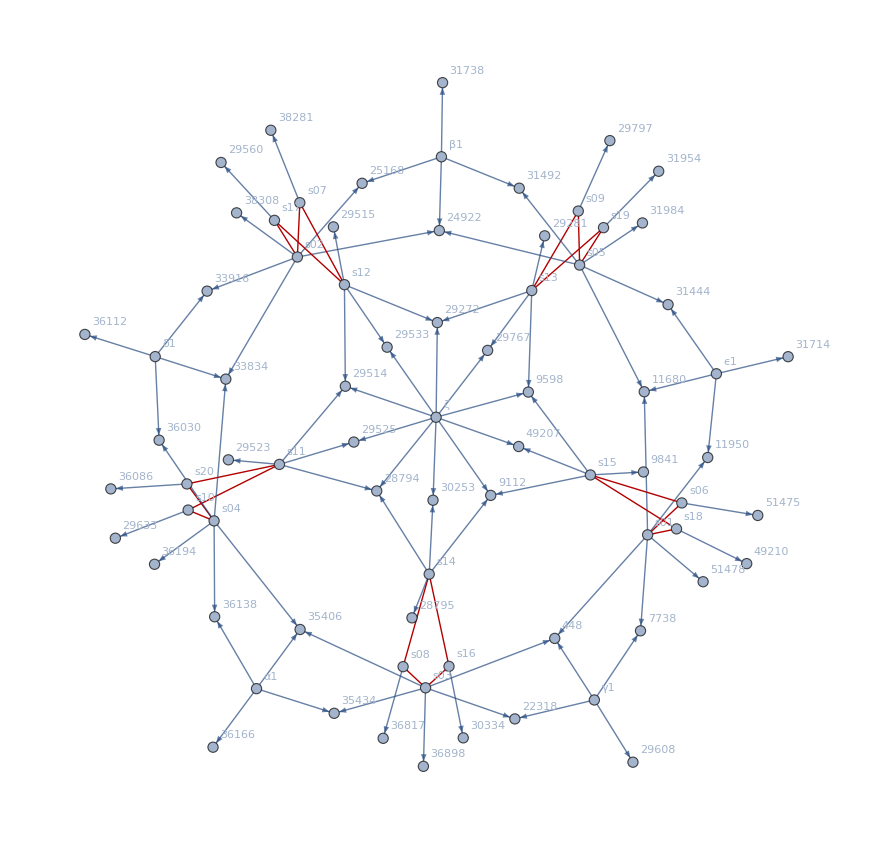

```mathematica
Graph[Join[edges1,edges2],GraphHighlight->edges2, VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

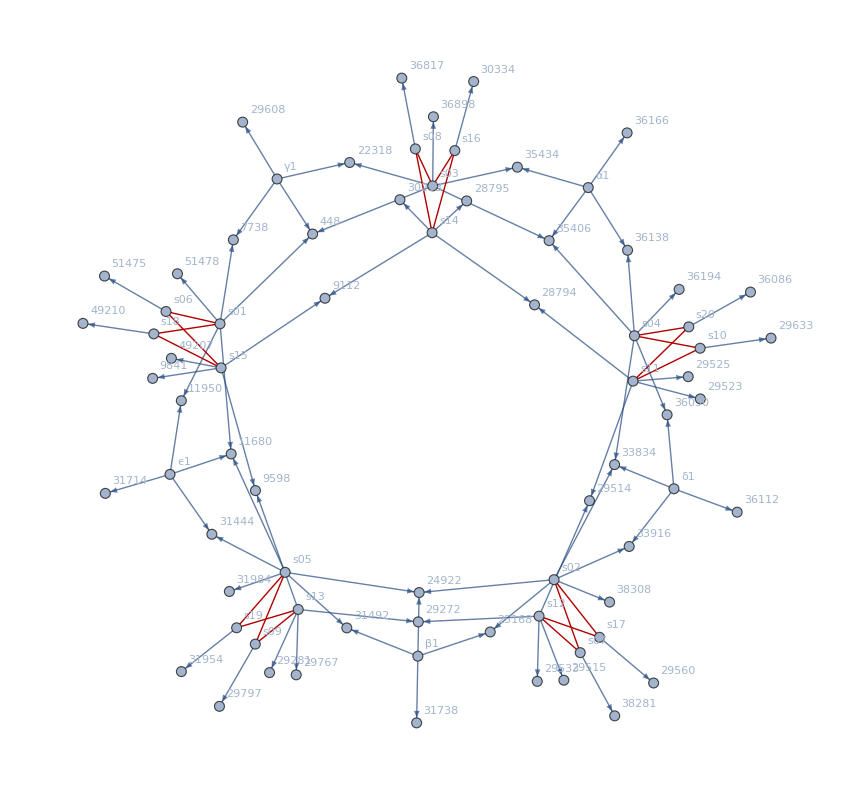

```mathematica
VertexDelete[Graph[Join[edges1,edges2],GraphHighlight->edges2, VertexLabels->"Name"],ζ]
```

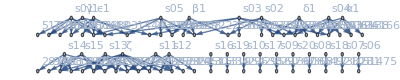

```mathematica
Graph[Table [Map[#->jj&,With[{kk=getAllVariables[test[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]]],{jj,Select[stubbornKeys,#≠K5Key&]}]//Flatten, VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

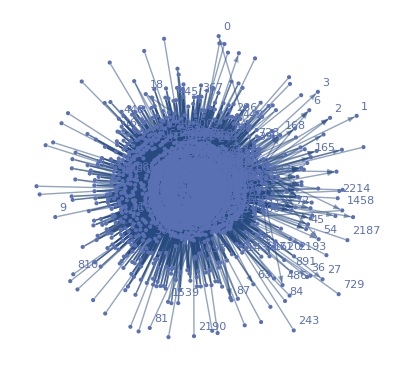

```mathematica
Graph[Table [Map[#->jj&,With[{kk=getAllVariables[test[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]]],{jj,Keys[test]}]//Flatten, VertexLabels->"Name"]
```

```mathematica
Table [jj->With[{kk=getAllVariables[test2[jj]["colofour3"]]},If[ListQ[kk],kk,{kk}]],{jj,stubbornKeys}]//TableForm
```

448→{s01,s03,γ1}
7738→{s01,γ1}
9112→{s14,s15,ζ}
9598→{s13,s15,ζ}
9841→{s15}
11680→{s01,s05,ϵ1}
11950→{s01,ϵ1}
22318→{s03,γ1}
24922→{s02,s05,β1}
25168→{s02,β1}
28794→{s11,s14,ζ}
28795→{s14}
29272→{s12,s13,ζ}
29281→{s13}
29514→{s11,s12,ζ}
29515→{s12}
29523→{s11}
29524→{ζ}
29525→{s11,ζ}
29533→{s12,ζ}
29560→{s17}
29608→{γ1}
29633→{s10}
29767→{s13,ζ}
29797→{s09}
30253→{s14,ζ}
30334→{s16}
31444→{s05,ϵ1}
31492→{s05,β1}
31714→{ϵ1}
31738→{β1}
31954→{s19}
31984→{s05}
33834→{s02,s04,δ1}
33916→{s02,δ1}
35406→{s03,s04,α1}
35434→{s03,α1}
36030→{s04,δ1}
36086→{s20}
36112→{δ1}
36138→{s04,α1}
36166→{α1}
36194→{s04}
36817→{s08}
36898→{s03}
38281→{s07}
38308→{s02}
49207→{s15,ζ}
49210→{s18}
51475→{s06}
51478→{s01}

```mathematica
With[
{vars={α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}},Select[Keys[test],ContainsAll[ListofVars[#],vars]&]//Length
]
```

858

```mathematica
ListofVars[x_]:=With[{kk=getAllVariables[test[x]["colofour2"]]},If[ListQ[kk],kk,{kk}]]
```

```mathematica
Sort[Tally[Flatten[Table[ListofVars[k],{k,Keys[test]}]]],#1[[2]]>#2[[2]]&]//TableForm
```

ϵ | 1468
δ | 1468
γ | 1468
β | 1468
α | 1468
ζ | 1439
b18 | 1421
b17 | 1421
b16 | 1421
b20 | 1421
b19 | 1421
b25 | 1397
b24 | 1397
b23 | 1397
b22 | 1397
b21 | 1397
ϵ1 | 1319
δ1 | 1319
γ1 | 1319
β1 | 1319
α1 | 1319
b38 | 1308
b36 | 1308
b40 | 1308
b39 | 1308
b37 | 1308
b03 | 1281
b01 | 1281
b05 | 1281
b02 | 1281
b04 | 1281
b27 | 1241
b30 | 1241
b29 | 1241
b28 | 1241
b26 | 1241
b10 | 1043
b09 | 1043
b08 | 1043
b07 | 1043
b06 | 1043
b15 | 696
b13 | 696
b14 | 696
b11 | 696
b12 | 696
b31 | 354
b32 | 354
b33 | 354
b35 | 354
b34 | 354
z | 52